## Project 1: Solving Kepler’s Equation

## Task 1:

```mathematica
Clear["Global`*"]
```

Functions of root finding algorithm for Kepler' s equation using the Newton - Raphson method.

```mathematica
KeplerEq[x_,M0_,e0_]:= Module[{Mpoints=M0,epoints=e0},x - Mpoints-epoints*Sin[x]]
KeplerDer[x0_,M0_,e0_]:= Module[{xpoint=x0,M=M0,e=e0},fdot[x_]=D[KeplerEq[x,M,e],x];fdot[xpoint]]
NewtonRaphson[x_,M0_,e0_]:=Module[{M=M0,e=e0},x-KeplerEq[x,M,e]/KeplerDer[x,M,e]]
```

Initialization of values : Mean anomaly M [0, 2 π], eccentricities e = 0.1, 0.3, 0.5, 0.7, 0.9, tolerance (negatice power of 10, e.g. 5 equals to 10^(-5)) and the list of solutions representing the values of Eccentric anomaly E.

```mathematica
Mp = Range[0.0,2*Pi,(2*Pi)/99];
ep = Range[0.1,0.9,0.2];
tol = 5;
points = {};
```

Implimentation of root solving algoritm

```mathematica
For[i=1,i ≤ Length[ep],i ++,For[ j=1,j≤ Length[Mp],j++,xn = Mp[[j]];xn1 = NewtonRaphson[xn,Mp[[j]],ep[[i]]];While[Abs[xn1-xn]>10^(-tol),xn=xn1; xn1=NewtonRaphson[xn,Mp[[j]],ep[[i]]]];AppendTo[points, {Mp[[j]],xn1}]]]
FinalPoints =Partition[points,Length[Mp]];
```

Plotting of the numerical results, using the Newton - Raphson method

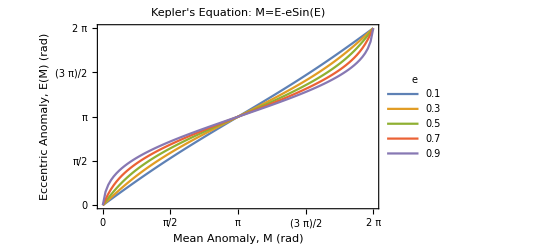

```mathematica
ListPlot[{FinalPoints[[1]],FinalPoints[[2]],FinalPoints[[3]],FinalPoints[[4]],FinalPoints[[5]]},Joined->True,PlotLegends->PointLegend[ep,LegendLabel->"e",LegendFunction->Frame],Frame->True,GridLines->{{0,π/2,π,3 π/2,2 π},{0,π/2,π,3 π/2,2 π}},FrameTicks-> {{{0,π/2,π,3 π/2,2 π},None},{{0,π/2,π,3 π/2,2 π},None}},FrameLabel->{"Mean Anomaly, M (rad)","Eccentric Anomaly, E(M) (rad)"},PlotLabel->"Kepler's Equation: M=E-eSin(E)"]
```

Save the plot of solutions for eccentricities e = 0.3 and e = 0.9 for later comparison of the results of Task 1 with the other Tasks 
(g1 plot is for e = 0.3 and g2 plot for e = 0.9)

```mathematica
g1=ListPlot[FinalPoints[[2]],Joined->True,PlotLegends->PointLegend[{ep[[2]]},LegendLabel->"Numerical",LegendFunction->Frame],Frame->True,GridLines->{{0,π/2,π,3 π/2,2 π},{0,π/2,π,3 π/2,2 π}},FrameTicks-> {{{0,π/2,π,3 π/2,2 π},None},{{0,π/2,π,3 π/2,2 π},None}},FrameLabel->{"Mean Anomaly, M (rad)","Eccentric Anomaly, E(M) (rad)"},PlotLabel->"Kepler's Equation: M=E-eSin(E)",PlotStyle->{Magenta}];
g2=ListPlot[FinalPoints[[5]],Joined->True,PlotLegends->PointLegend[{ep[[5]]},LegendLabel->"Numerical",LegendFunction->Frame],Frame->True,GridLines->{{0,π/2,π,3 π/2,2 π},{0,π/2,π,3 π/2,2 π}},FrameTicks-> {{{0,π/2,π,3 π/2,2 π},None},{{0,π/2,π,3 π/2,2 π},None}},FrameLabel->{"Mean Anomaly, M (rad)","Eccentric Anomaly, E(M) (rad)"},PlotLabel->"Kepler's Equation: M=E-eSin(E)",PlotStyle->{Magenta}];
```

## Task 2:

Functions that apply the Lagrange' s theroem to Kepler' s equation and calculates the series solution

```mathematica
Deriv[M_,i_]:=Module[{n=i},D[Sin[M]^n,{M,i-1}]]
Lagrange[y_,M_,e_,n_]:=Module[{n0=n,a=M},For[i=1,i≤n0,i++,o=((e^i)/(i!))*Deriv[M,i];a=o+a];a]
```

Computation of series expression E (M)  by keeping terms up to order n1 = 3 and n2 = 10

```mathematica
n1=3;
n2=10;
E3=Lagrange[y,M,e,n1]//N//TrigReduce
E10=Lagrange[y,M,e,n2]//N//TrigReduce//FullSimplify
```

M+e Sin[M]-0.125 e^3 Sin[M]+0.5 e^2 Sin[2 M]+0.375 e^3 Sin[3 M]

M+(e-0.125 e^3+0.00520833 e^5-0.000108507 e^7+1.35634×10^-6 e^9) Sin[M]+e^2 (0.5-0.166667 e^2+0.0208333 e^4-0.00138889 e^6+0.0000578704 e^8) Sin[2 M]+e^3 ((0.375-0.210938 e^2+0.0474609 e^4-0.00593262 e^6) Sin[3 M]+e ((0.333333-0.266667 e^2+0.0888889 e^4-0.0169312 e^6) Sin[4 M]+e ((0.325521-0.339084 e^2+0.151377 e^4) Sin[5 M]+e ((0.3375-0.433929 e^2+0.244085 e^4) Sin[6 M]+e ((0.364735-0.558501 e^2) Sin[7 M]+e ((0.406349-0.722399 e^2) Sin[8 M]+e (0.46338 Sin[9 M]+0.538229 e Sin[10 M])))))))

Evaluation of order n = 3 and n = 10 for e = 0.3

```mathematica
E1 = E3/.e->0.3//TrigReduce
E2 = E10/.e->0.3//TrigReduce
```

M+0.296625 Sin[M]+0.045 Sin[2 M]+0.010125 Sin[3 M]

M+0.296638 Sin[M]+0.0436651 Sin[2 M]+0.00962268 Sin[3 M]+0.00251133 Sin[4 M]+0.000719837 Sin[5 M]+0.000219009 Sin[6 M]+0.0000687746 Sin[7 M]+0.0000223949 Sin[8 M]+9.1207×10^-6 Sin[9 M]+3.17819×10^-6 Sin[10 M]

Plotting of the series expansion for order 3 and 10 for e = 0.3

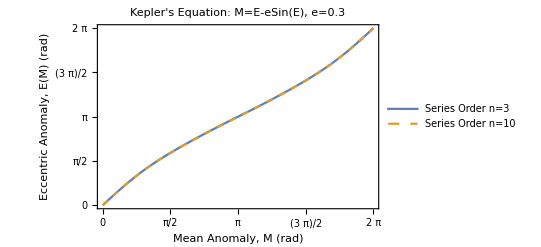

```mathematica
g3=Plot[{E1,E2},{M,0,2*Pi},Frame->True,GridLines->{{0,π/2,π,3 π/2,2 π},{0,π/2,π,3 π/2,2 π}},PlotLabel->"Kepler's Equation: M=E-eSin(E), e=0.3",FrameLabel->{"Mean Anomaly, M (rad)","Eccentric Anomaly, E(M) (rad)"},PlotLegends->LineLegend[{"Series Order n=3","Series Order n=10"},LegendFunction->Frame],FrameTicks-> {{{0,π/2,π,3 π/2,2 π},None},{{0,π/2,π,3 π/2,2 π},None}},PlotStyle->{Automatic,Dashed}]
```

Evaluation and plotting of the series expansion of order n = 3 and n = 10 for e = 0.9

M+0.808875 Sin[M]+0.405 Sin[2 M]+0.273375 Sin[3 M]

M+0.811899 Sin[M]+0.306144 Sin[2 M]+0.169221 Sin[3 M]+0.109343 Sin[4 M]+0.0886804 Sin[5 M]+0.0776764 Sin[6 M]-0.0419229 Sin[7 M]-0.0769648 Sin[8 M]+0.179523 Sin[9 M]+0.187669 Sin[10 M]

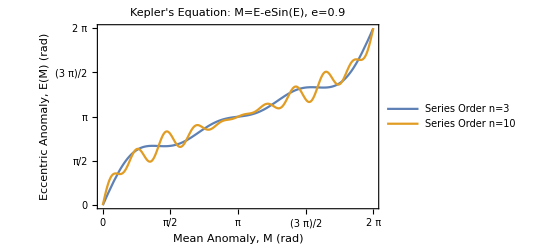

```mathematica
E1 = E3/.e->0.9//TrigReduce
E2 = E10/.e->0.9//TrigReduce
g4=Plot[{E1/.e-> 0.9,E2/.e-> 0.9},{M,0,2*Pi},Frame->True,GridLines->{{0,π/2,π,3 π/2,2 π},{0,π/2,π,3 π/2,2 π}},FrameTicks-> {{{0,π/2,π,3 π/2,2 π},None},{{0,π/2,π,3 π/2,2 π},None}},PlotLabel->"Kepler's Equation: M=E-eSin(E), e=0.9",FrameLabel->{"Mean Anomaly, M (rad)","Eccentric Anomaly, E(M) (rad)"},PlotLegends->LineLegend[{"Series Order n=3","Series Order n=10"},LegendFunction->Frame]]
```

Comparison of series expansion with the numerical results of Task1

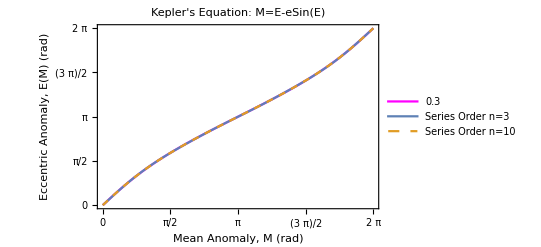

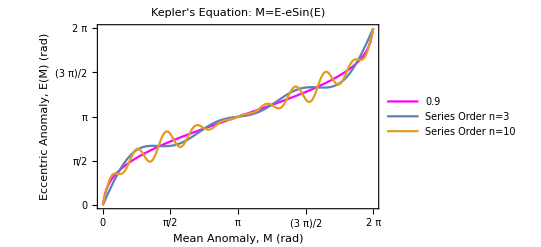

```mathematica
Show[g1,g3]
Show[g2,g4]
```

Lagrange’s work on Kepler’s equation produced a solution as a power series in the eccentricity e with coefficients which are linear combinations of trigonometric functions of integral multiples of the mean anomaly. Plotting the solutions of Task2 and comparing it with the numerical results of Task1, is evident that for eccentricity e = 0.3 Langrange’s series converges while for e = 0.9 diverges. Hence there is some critical value, which is approximately equal to 0.6, and for eccentricities smaller than this critical value the Lagrange’s series converges while for larger values it is divarges.

## Task 3 :

Functions : The first function computes the Bessel function Jn (x) and the second implements the Fourier - Bessel expansion of E

```mathematica
BesselF[e_,i_]:=Module[{n=i,J=0,x=e},For[k=0,k≤100,k++,J1=(((-1)^k)/((Factorial[k])*(Factorial[n+k])))*((x)/2)^(n+2*k);J=J1+J];J]
FourierBessel[y_,M_,e_,n_]:=Module[{n0=n,a=M},For[i=1.0,i≤n0,i++,o=(2/i)*BesselF[i*e,i]*Sin[i*M];a=o+a];a]
```

Computation of the Bessel functions Jn (x) and plotting of the functions J1, J2, ..., J5 for x = [0, 15]

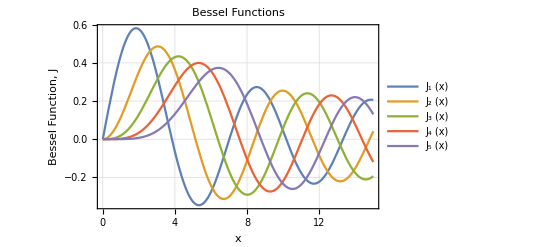

```mathematica
Jp={};
For[i=1,i≤ 5,i++,AppendTo[Jp,BesselF[e,i]]]
Plot[{Jp[[1]],Jp[[2]],Jp[[3]],Jp[[4]],Jp[[5]]},{e,0,15},Frame->True,GridLines->Automatic,PlotLabel->"Bessel Functions",FrameLabel->{"x","Bessel Function, J"},PlotLegends->LineLegend[{Subscript[J,1]"(x)",Subscript[J,2]"(x)",Subscript[J,3]"(x)",Subscript[J,4]"(x)",Subscript[J,5]"(x)"},LegendFunction->Frame]]
```

Computation of the Fourier-Bessel series expansion keeping up terms up to j=3 and for e = 0.3, e = 0.9  evaluation of E(M) from the order three series

```mathematica
J1=FourierBessel[y,M,e,3]//N
J11=J1/.e->0.3
J21=J1/.e->0.9
```

M+2. (0.5 e^1.-0.0625 e^3.+0.00260417 e^5.-0.0000542535 e^7.+6.78168×10^-7 e^9.-5.6514×10^-9 e^11.+3.36393×10^-11 e^13.-1.50175×10^-13 e^15.+5.21443×10^-16 e^17.-1.44845×10^-18 e^19.+3.29194×10^-21 e^21.-6.23473×10^-24 e^23.+9.99155×10^-27 e^25.-1.37247×10^-29 e^27.+1.63389×10^-32 e^29.-1.70197×10^-35 e^31.+1.56431×10^-38 e^33.-1.27803×10^-41 e^35.+9.34232×10^-45 e^37.-6.14626×10^-48 e^39.+3.65849×10^-51 e^41.-1.9797×10^-54 e^43.+9.78113×10^-58 e^45.-4.42986×10^-61 e^47.+1.84578×10^-64 e^49.-7.09914×10^-68 e^51.+2.52818×10^-71 e^53.-8.36039×10^-75 e^55.+2.57401×10^-78 e^57.-7.39659×10^-82 e^59.+1.98833×10^-85 e^61.-5.01091×10^-89 e^63.+1.1863×10^-92 e^65.-2.64326×10^-96 e^67.+5.55307×10^-100 e^69.-1.1018×10^-103 e^71.+2.06794×10^-107 e^73.-3.67699×10^-111 e^75.+6.20276×10^-115 e^77.-9.94032×10^-119 e^79.+1.51529×10^-122 e^81.-2.1999×10^-126 e^83.+3.04527×10^-130 e^85.-4.02387×10^-134 e^87.+5.08065×10^-138 e^89.-6.13605×10^-142 e^91.+7.09534×10^-146 e^93.-7.86274×10^-150 e^95.+8.35751×10^-154 e^97.-8.52807×10^-158 e^99.+8.36085×10^-162 e^101.-7.88165×10^-166 e^103.+7.14954×10^-170 e^105.-6.24523×10^-174 e^107.+5.25692×10^-178 e^109.-4.26698×10^-182 e^111.+3.34194×10^-186 e^113.-2.52718×10^-190 e^115.+1.84627×10^-194 e^117.-1.30386×10^-198 e^119.+8.90617×10^-203 e^121.-5.88721×10^-207 e^123.+3.76806×10^-211 e^125.-2.33634×10^-215 e^127.+1.40405×10^-219 e^129.-8.18213×10^-224 e^131.+4.62581×10^-228 e^133.-2.5383×10^-232 e^135.+1.35246×10^-236 e^137.-7.00033×10^-241 e^139.+3.52129×10^-245 e^141.-1.72207×10^-249 e^143.+8.19098×10^-254 e^145.-3.79072×10^-258 e^147.+1.70753×10^-262 e^149.-7.48917×10^-267 e^151.+3.19941×10^-271 e^153.-1.33175×10^-275 e^155.+5.40309×10^-280 e^157.-2.1373×10^-284 e^159.+8.24575×10^-289 e^161.-3.10364×10^-293 e^163.+1.14004×10^-297 e^165.-4.08792×10^-302 e^167.+1.43134×10^-306 e^169.-4.89515552465021×10^-311 e^171.+1.63564405394614×10^-315 e^173.-5.34105294522657×10^-320 e^175.+1.70488155810356×10^-324 e^177.-5.32110348971126×10^-329 e^179.+1.62426846450273×10^-333 e^181.-4.85030000150118×10^-338 e^183.+1.41722183307076×10^-342 e^185.-4.05291075575039×10^-347 e^187.+1.1346334702549×10^-351 e^189.-3.11028911802311×10^-356 e^191.+8.35021777819772×10^-361 e^193.-2.19603875925679×10^-365 e^195.+5.65872696159749×10^-370 e^197.-1.42897145494889×10^-374 e^199.+3.53705805680433×10^-379 e^201.) Sin[1. M]+1. (0.5 e^2.-0.166667 e^4.+0.0208333 e^6.-0.00138889 e^8.+0.0000578704 e^10.-1.65344×10^-6 e^12.+3.44466×10^-8 e^14.-5.46772×10^-10 e^16.+6.83465×10^-12 e^18.-6.90369×10^-14 e^20.+5.75307×10^-16 e^22.-4.02313×10^-18 e^24.+2.39472×10^-20 e^26.-1.22806×10^-22 e^28.+5.48242×10^-25 e^30.-2.14997×10^-27 e^32.+7.46516×10^-30 e^34.-2.3112×10^-32 e^36.+6.41999×10^-35 e^38.-1.60902×10^-37 e^40.+3.65686×10^-40 e^42.-7.57115×10^-43 e^44.+1.43393×10^-45 e^46.-2.49379×10^-48 e^48.+3.99646×10^-51 e^50.-5.92068×10^-54 e^52.+8.1328×10^-57 e^54.-1.03867×10^-59 e^56.+1.23651×10^-62 e^58.-1.37543×10^-65 e^60.+1.43274×10^-68 e^62.-1.40053×10^-71 e^64.+1.28725×10^-74 e^66.-1.1145×10^-77 e^68.+9.10543×10^-81 e^70.-7.03122×10^-84 e^72.+5.13978×10^-87 e^74.-3.56187×10^-90 e^76.+2.34334×10^-93 e^78.-1.4655×10^-96 e^80.+8.72322×10^-100 e^82.-4.94794×10^-103 e^84.+2.67746×10^-106 e^86.-1.3837×10^-109 e^88.+6.83646×10^-113 e^90.-3.23237×10^-116 e^92.+1.46393×10^-119 e^94.-6.35664×10^-123 e^96.+2.6486×10^-126 e^98.-1.05986×10^-129 e^100.+4.0764×10^-133 e^102.-1.5081×10^-136 e^104.+5.37073×10^-140 e^106.-1.84245×10^-143 e^108.+6.09275×10^-147 e^110.-1.94346×10^-150 e^112.+5.98356×10^-154 e^114.-1.77923×10^-157 e^116.+5.11274×10^-161 e^118.-1.4206×10^-164 e^120.+3.81882×10^-168 e^122.-9.93707×10^-172 e^124.+2.5043×10^-175 e^126.-6.11551×10^-179 e^128.+1.4478×10^-182 e^130.-3.32446×10^-186 e^132.+7.40744×10^-190 e^134.-1.6023×10^-193 e^136.+3.36618×10^-197 e^138.-6.87115×10^-201 e^140.+1.36332×10^-204 e^142.-2.63038×10^-208 e^144.+4.93689×10^-212 e^146.-9.01715×10^-216 e^148.+1.60333×10^-219 e^150.-2.77634×10^-223 e^152.+4.68343×10^-227 e^154.-7.69921×10^-231 e^156.+1.23385×10^-234 e^158.-1.92819×10^-238 e^160.+2.93931×10^-242 e^162.-4.37202×10^-246 e^164.+6.34731×10^-250 e^166.-8.99689×10^-254 e^168.+1.24542×10^-257 e^170.-1.68413×10^-261 e^172.+2.22533×10^-265 e^174.-2.874×10^-269 e^176.+3.62878×10^-273 e^178.-4.48053×10^-277 e^180.+5.41127×10^-281 e^182.-6.39403×10^-285 e^184.+7.39365×10^-289 e^186.-8.3686×10^-293 e^188.+9.27371×10^-297 e^190.-1.00637×10^-300 e^192.+1.0697×10^-304 e^194.-1.11391989549147×10^-308 e^196.+1.13665295458316×10^-312 e^198.-1.13676663124633×10^-316 e^200.+1.11447708945712×10^-320 e^202.) Sin[2. M]+0.666667 (0.5625 e^3.-0.316406 e^5.+0.0711914 e^7.-0.00889893 e^9.+0.000715092 e^11.-0.0000402239 e^13.+1.676×10^-6 e^15.-5.38713×10^-8 e^17.+1.37739×10^-9 e^19.-2.86957×10^-11 e^21.+4.96656×10^-13 e^23.-7.25634×10^-15 e^25.+9.07042×10^-17 e^27.-9.81175×10^-19 e^29.+9.27582×10^-21 e^31.-7.72985×10^-23 e^33.+5.7211×10^-25 e^35.-3.78602×10^-27 e^37.+2.25359×10^-29 e^39.-1.21305×10^-31 e^41.+5.93342×10^-34 e^43.-2.64885×10^-36 e^45.+1.08362×10^-38 e^47.-4.07716×10^-41 e^49.+1.41568×10^-43 e^51.-4.55041×10^-46 e^53.+1.35788×10^-48 e^55.-3.77189×10^-51 e^57.+9.77736×10^-54 e^59.-2.37059×10^-56 e^61.+5.3877×10^-59 e^63.-1.15013×10^-61 e^65.+2.31052×10^-64 e^67.-4.37599×10^-67 e^69.+7.82669×10^-70 e^71.-1.32406×10^-72 e^73.+2.1219×10^-75 e^75.-3.22586×10^-78 e^77.+4.65865×10^-81 e^79.-6.39924×10^-84 e^81.+8.3711×10^-87 e^83.-1.04407×10^-89 e^85.+1.24294×10^-92 e^87.-1.41386×10^-95 e^89.+1.53829×10^-98 e^91.-1.60238×10^-101 e^93.+1.59954×10^-104 e^95.-1.53147×10^-107 e^97.+1.40761×10^-110 e^99.-1.24298×10^-113 e^101.+1.05536×10^-116 e^103.-8.62222×10^-120 e^105.+6.78322×10^-123 e^107.-5.14226×10^-126 e^109.+3.75896×10^-129 e^111.-2.65131×10^-132 e^113.+1.80552×10^-135 e^115.-1.18784×10^-138 e^117.+7.55411×10^-142 e^119.-4.64646×10^-145 e^121.+2.76575×10^-148 e^123.-1.59399×10^-151 e^125.+8.89945×10^-155 e^127.-4.81572×10^-158 e^129.+2.52691×10^-161 e^131.-1.28632×10^-164 e^133.+6.35534×10^-168 e^135.-3.04894×10^-171 e^137.+1.4209×10^-174 e^139.-6.43524×10^-178 e^141.+2.83352×10^-181 e^143.-1.21344×10^-184 e^145.+5.056×10^-188 e^147.-2.05047×10^-191 e^149.+8.0968×10^-195 e^151.-3.11416×10^-198 e^153.+1.16703×10^-201 e^155.-4.26269×10^-205 e^157.+1.51805×10^-208 e^159.-5.27264×10^-212 e^161.+1.78666×10^-215 e^163.-5.90828×10^-219 e^165.+1.90726×10^-222 e^167.-6.01197×10^-226 e^169.+1.85098×10^-229 e^171.-5.56777×10^-233 e^173.+1.63672×10^-236 e^175.-4.70323×10^-240 e^177.+1.32146×10^-243 e^179.-3.63128×10^-247 e^181.+9.7615×10^-251 e^183.-2.56762×10^-254 e^185.+6.60999×10^-258 e^187.-1.66582×10^-261 e^189.+4.11067×10^-265 e^191.-9.93448×10^-269 e^193.+2.35191×10^-272 e^195.-5.45547×10^-276 e^197.+1.24013×10^-279 e^199.-2.76321×10^-283 e^201.+6.03614×10^-287 e^203.) Sin[3. M]

M+0.296638 Sin[1. M]+0.0436651 Sin[2. M]+0.00962269 Sin[3. M]

M+0.811899 Sin[1. M]+0.306144 Sin[2. M]+0.169364 Sin[3. M]

Computation of the Fourier - Bessel series expansion keeping up terms up to j = 10 and for e = 0.3, e = 0.9 evaluation of E (M) from the order ten series

```mathematica
J2=FourierBessel[y,M,e,10]//N
J12=J2/.e->0.3
J22=J2/.e->0.9
```

M+2. (0.5 e^1.-0.0625 e^3.+0.00260417 e^5.-0.0000542535 e^7.+6.78168×10^-7 e^9.-5.6514×10^-9 e^11.+3.36393×10^-11 e^13.-1.50175×10^-13 e^15.+5.21443×10^-16 e^17.-1.44845×10^-18 e^19.+3.29194×10^-21 e^21.-6.23473×10^-24 e^23.+9.99155×10^-27 e^25.-1.37247×10^-29 e^27.+1.63389×10^-32 e^29.-1.70197×10^-35 e^31.+1.56431×10^-38 e^33.-1.27803×10^-41 e^35.+9.34232×10^-45 e^37.-6.14626×10^-48 e^39.+3.65849×10^-51 e^41.-1.9797×10^-54 e^43.+9.78113×10^-58 e^45.-4.42986×10^-61 e^47.+1.84578×10^-64 e^49.-7.09914×10^-68 e^51.+2.52818×10^-71 e^53.-8.36039×10^-75 e^55.+2.57401×10^-78 e^57.-7.39659×10^-82 e^59.+1.98833×10^-85 e^61.-5.01091×10^-89 e^63.+1.1863×10^-92 e^65.-2.64326×10^-96 e^67.+5.55307×10^-100 e^69.-1.1018×10^-103 e^71.+2.06794×10^-107 e^73.-3.67699×10^-111 e^75.+6.20276×10^-115 e^77.-9.94032×10^-119 e^79.+1.51529×10^-122 e^81.-2.1999×10^-126 e^83.+3.04527×10^-130 e^85.-4.02387×10^-134 e^87.+5.08065×10^-138 e^89.-6.13605×10^-142 e^91.+7.09534×10^-146 e^93.-7.86274×10^-150 e^95.+8.35751×10^-154 e^97.-8.52807×10^-158 e^99.+8.36085×10^-162 e^101.-7.88165×10^-166 e^103.+7.14954×10^-170 e^105.-6.24523×10^-174 e^107.+5.25692×10^-178 e^109.-4.26698×10^-182 e^111.+3.34194×10^-186 e^113.-2.52718×10^-190 e^115.+1.84627×10^-194 e^117.-1.30386×10^-198 e^119.+8.90617×10^-203 e^121.-5.88721×10^-207 e^123.+3.76806×10^-211 e^125.-2.33634×10^-215 e^127.+1.40405×10^-219 e^129.-8.18213×10^-224 e^131.+4.62581×10^-228 e^133.-2.5383×10^-232 e^135.+1.35246×10^-236 e^137.-7.00033×10^-241 e^139.+3.52129×10^-245 e^141.-1.72207×10^-249 e^143.+8.19098×10^-254 e^145.-3.79072×10^-258 e^147.+1.70753×10^-262 e^149.-7.48917×10^-267 e^151.+3.19941×10^-271 e^153.-1.33175×10^-275 e^155.+5.40309×10^-280 e^157.-2.1373×10^-284 e^159.+8.24575×10^-289 e^161.-3.10364×10^-293 e^163.+1.14004×10^-297 e^165.-4.08792×10^-302 e^167.+1.43134×10^-306 e^169.-4.89515552465021×10^-311 e^171.+1.63564405394614×10^-315 e^173.-5.34105294522657×10^-320 e^175.+1.70488155810356×10^-324 e^177.-5.32110348971126×10^-329 e^179.+1.62426846450273×10^-333 e^181.-4.85030000150118×10^-338 e^183.+1.41722183307076×10^-342 e^185.-4.05291075575039×10^-347 e^187.+1.1346334702549×10^-351 e^189.-3.11028911802311×10^-356 e^191.+8.35021777819772×10^-361 e^193.-2.19603875925679×10^-365 e^195.+5.65872696159749×10^-370 e^197.-1.42897145494889×10^-374 e^199.+3.53705805680433×10^-379 e^201.) Sin[1. M]+1. (0.5 e^2.-0.166667 e^4.+0.0208333 e^6.-0.00138889 e^8.+0.0000578704 e^10.-1.65344×10^-6 e^12.+3.44466×10^-8 e^14.-5.46772×10^-10 e^16.+6.83465×10^-12 e^18.-6.90369×10^-14 e^20.+5.75307×10^-16 e^22.-4.02313×10^-18 e^24.+2.39472×10^-20 e^26.-1.22806×10^-22 e^28.+5.48242×10^-25 e^30.-2.14997×10^-27 e^32.+7.46516×10^-30 e^34.-2.3112×10^-32 e^36.+6.41999×10^-35 e^38.-1.60902×10^-37 e^40.+3.65686×10^-40 e^42.-7.57115×10^-43 e^44.+1.43393×10^-45 e^46.-2.49379×10^-48 e^48.+3.99646×10^-51 e^50.-5.92068×10^-54 e^52.+8.1328×10^-57 e^54.-1.03867×10^-59 e^56.+1.23651×10^-62 e^58.-1.37543×10^-65 e^60.+1.43274×10^-68 e^62.-1.40053×10^-71 e^64.+1.28725×10^-74 e^66.-1.1145×10^-77 e^68.+9.10543×10^-81 e^70.-7.03122×10^-84 e^72.+5.13978×10^-87 e^74.-3.56187×10^-90 e^76.+2.34334×10^-93 e^78.-1.4655×10^-96 e^80.+8.72322×10^-100 e^82.-4.94794×10^-103 e^84.+2.67746×10^-106 e^86.-1.3837×10^-109 e^88.+6.83646×10^-113 e^90.-3.23237×10^-116 e^92.+1.46393×10^-119 e^94.-6.35664×10^-123 e^96.+2.6486×10^-126 e^98.-1.05986×10^-129 e^100.+4.0764×10^-133 e^102.-1.5081×10^-136 e^104.+5.37073×10^-140 e^106.-1.84245×10^-143 e^108.+6.09275×10^-147 e^110.-1.94346×10^-150 e^112.+5.98356×10^-154 e^114.-1.77923×10^-157 e^116.+5.11274×10^-161 e^118.-1.4206×10^-164 e^120.+3.81882×10^-168 e^122.-9.93707×10^-172 e^124.+2.5043×10^-175 e^126.-6.11551×10^-179 e^128.+1.4478×10^-182 e^130.-3.32446×10^-186 e^132.+7.40744×10^-190 e^134.-1.6023×10^-193 e^136.+3.36618×10^-197 e^138.-6.87115×10^-201 e^140.+1.36332×10^-204 e^142.-2.63038×10^-208 e^144.+4.93689×10^-212 e^146.-9.01715×10^-216 e^148.+1.60333×10^-219 e^150.-2.77634×10^-223 e^152.+4.68343×10^-227 e^154.-7.69921×10^-231 e^156.+1.23385×10^-234 e^158.-1.92819×10^-238 e^160.+2.93931×10^-242 e^162.-4.37202×10^-246 e^164.+6.34731×10^-250 e^166.-8.99689×10^-254 e^168.+1.24542×10^-257 e^170.-1.68413×10^-261 e^172.+2.22533×10^-265 e^174.-2.874×10^-269 e^176.+3.62878×10^-273 e^178.-4.48053×10^-277 e^180.+5.41127×10^-281 e^182.-6.39403×10^-285 e^184.+7.39365×10^-289 e^186.-8.3686×10^-293 e^188.+9.27371×10^-297 e^190.-1.00637×10^-300 e^192.+1.0697×10^-304 e^194.-1.11391989549147×10^-308 e^196.+1.13665295458316×10^-312 e^198.-1.13676663124633×10^-316 e^200.+1.11447708945712×10^-320 e^202.) Sin[2. M]+0.666667 (0.5625 e^3.-0.316406 e^5.+0.0711914 e^7.-0.00889893 e^9.+0.000715092 e^11.-0.0000402239 e^13.+1.676×10^-6 e^15.-5.38713×10^-8 e^17.+1.37739×10^-9 e^19.-2.86957×10^-11 e^21.+4.96656×10^-13 e^23.-7.25634×10^-15 e^25.+9.07042×10^-17 e^27.-9.81175×10^-19 e^29.+9.27582×10^-21 e^31.-7.72985×10^-23 e^33.+5.7211×10^-25 e^35.-3.78602×10^-27 e^37.+2.25359×10^-29 e^39.-1.21305×10^-31 e^41.+5.93342×10^-34 e^43.-2.64885×10^-36 e^45.+1.08362×10^-38 e^47.-4.07716×10^-41 e^49.+1.41568×10^-43 e^51.-4.55041×10^-46 e^53.+1.35788×10^-48 e^55.-3.77189×10^-51 e^57.+9.77736×10^-54 e^59.-2.37059×10^-56 e^61.+5.3877×10^-59 e^63.-1.15013×10^-61 e^65.+2.31052×10^-64 e^67.-4.37599×10^-67 e^69.+7.82669×10^-70 e^71.-1.32406×10^-72 e^73.+2.1219×10^-75 e^75.-3.22586×10^-78 e^77.+4.65865×10^-81 e^79.-6.39924×10^-84 e^81.+8.3711×10^-87 e^83.-1.04407×10^-89 e^85.+1.24294×10^-92 e^87.-1.41386×10^-95 e^89.+1.53829×10^-98 e^91.-1.60238×10^-101 e^93.+1.59954×10^-104 e^95.-1.53147×10^-107 e^97.+1.40761×10^-110 e^99.-1.24298×10^-113 e^101.+1.05536×10^-116 e^103.-8.62222×10^-120 e^105.+6.78322×10^-123 e^107.-5.14226×10^-126 e^109.+3.75896×10^-129 e^111.-2.65131×10^-132 e^113.+1.80552×10^-135 e^115.-1.18784×10^-138 e^117.+7.55411×10^-142 e^119.-4.64646×10^-145 e^121.+2.76575×10^-148 e^123.-1.59399×10^-151 e^125.+8.89945×10^-155 e^127.-4.81572×10^-158 e^129.+2.52691×10^-161 e^131.-1.28632×10^-164 e^133.+6.35534×10^-168 e^135.-3.04894×10^-171 e^137.+1.4209×10^-174 e^139.-6.43524×10^-178 e^141.+2.83352×10^-181 e^143.-1.21344×10^-184 e^145.+5.056×10^-188 e^147.-2.05047×10^-191 e^149.+8.0968×10^-195 e^151.-3.11416×10^-198 e^153.+1.16703×10^-201 e^155.-4.26269×10^-205 e^157.+1.51805×10^-208 e^159.-5.27264×10^-212 e^161.+1.78666×10^-215 e^163.-5.90828×10^-219 e^165.+1.90726×10^-222 e^167.-6.01197×10^-226 e^169.+1.85098×10^-229 e^171.-5.56777×10^-233 e^173.+1.63672×10^-236 e^175.-4.70323×10^-240 e^177.+1.32146×10^-243 e^179.-3.63128×10^-247 e^181.+9.7615×10^-251 e^183.-2.56762×10^-254 e^185.+6.60999×10^-258 e^187.-1.66582×10^-261 e^189.+4.11067×10^-265 e^191.-9.93448×10^-269 e^193.+2.35191×10^-272 e^195.-5.45547×10^-276 e^197.+1.24013×10^-279 e^199.-2.76321×10^-283 e^201.+6.03614×10^-287 e^203.) Sin[3. M]+0.5 (0.666667 e^4.-0.533333 e^6.+0.177778 e^8.-0.0338624 e^10.+0.0042328 e^12.-0.000376249 e^14.+0.0000250833 e^16.-1.30303×10^-6 e^18.+5.42928×10^-8 e^20.-1.85616×10^-9 e^22.+5.30333×10^-11 e^24.-1.28566×10^-12 e^26.+2.67845×10^-14 e^28.-4.84787×10^-16 e^30.+7.69503×10^-18 e^32.-1.08×10^-19 e^34.+1.35001×10^-21 e^36.-1.51261×10^-23 e^38.+1.52789×10^-25 e^40.-1.39853×10^-27 e^42.+1.16544×10^-29 e^44.-8.87953×10^-32 e^46.+6.20946×10^-34 e^48.-3.99966×10^-36 e^50.+2.38075×10^-38 e^52.-1.31352×10^-40 e^54.+6.73598×10^-43 e^56.-3.21911×10^-45 e^58.+1.4371×10^-47 e^60.-6.00669×10^-50 e^62.+2.35556×10^-52 e^64.-8.68411×10^-55 e^66.+3.01532×10^-57 e^68.-9.87818×10^-60 e^70.+3.05826×10^-62 e^72.-8.96194×10^-65 e^74.+2.48943×10^-67 e^76.-6.56408×10^-70 e^78.+1.64513×10^-72 e^80.-3.92399×10^-75 e^82.+8.91816×10^-78 e^84.-1.93348×10^-80 e^86.+4.00306×10^-83 e^88.-7.92292×10^-86 e^90.+1.50055×10^-88 e^92.-2.72209×10^-91 e^94.+4.73407×10^-94 e^96.-7.9×10^-97 e^98.+1.26603×10^-99 e^100.-1.94998×10^-102 e^102.+2.88886×10^-105 e^104.-4.11959×10^-108 e^106.+5.65877×10^-111 e^108.-7.49258×10^-114 e^110.+9.56907×10^-117 e^112.-1.17955×10^-119 e^114.+1.40422×10^-122 e^116.-1.61544×10^-125 e^118.+1.79693×10^-128 e^120.-1.93374×10^-131 e^122.+2.01432×10^-134 e^124.-2.0321×10^-137 e^126.+1.98641×10^-140 e^128.-1.88241×10^-143 e^130.+1.73015×10^-146 e^132.-1.54306×10^-149 e^134.+1.33598×10^-152 e^136.-1.12338×10^-155 e^138.+9.17795×10^-159 e^140.-7.28842×10^-162 e^142.+5.62813×10^-165 e^144.-4.2277×10^-168 e^146.+3.09042×10^-171 e^148.-2.1992×10^-174 e^150.+1.52405×10^-177 e^152.-1.02889×10^-180 e^154.+6.76903×10^-184 e^156.-4.34121×10^-187 e^158.+2.71495×10^-190 e^160.-1.65622×10^-193 e^162.+9.85843×10^-197 e^164.-5.72748×10^-200 e^166.+3.24871×10^-203 e^168.-1.79959×10^-206 e^170.+9.73805×10^-210 e^172.-5.149×10^-213 e^174.+2.66098×10^-216 e^176.-1.34444×10^-219 e^178.+6.64249×10^-223 e^180.-3.2101×10^-226 e^182.+1.51778×10^-229 e^184.-7.02268×10^-233 e^186.+3.18056×10^-236 e^188.-1.41029×10^-239 e^190.+6.12371×10^-243 e^192.-2.60445×10^-246 e^194.+1.08519×10^-249 e^196.-4.43069×10^-253 e^198.+1.77299×10^-256 e^200.-6.95493×10^-260 e^202.+2.67497×10^-263 e^204.) Sin[4. M]+0.4 (0.813802 e^5.-0.847711 e^7.+0.378442 e^9.-0.0985527 e^11.+0.0171098 e^13.-0.00213873 e^15.+0.000202531 e^17.-0.0000150693 e^19.+9.05606×10^-7 e^21.-4.49209×10^-8 e^23.+1.87171×10^-9 e^25.-6.64668×10^-11 e^27.+2.03636×10^-12 e^29.-5.439×10^-14 e^31.+1.27796×10^-15 e^33.-2.66242×10^-17 e^35.+4.95241×10^-19 e^37.-8.27609×10^-21 e^39.+1.24941×10^-22 e^41.-1.71246×10^-24 e^43.+2.14057×10^-26 e^45.-2.45029×10^-28 e^47.+2.57817×10^-30 e^49.-2.5021×10^-32 e^51.+2.24686×10^-34 e^53.-1.87238×10^-36 e^55.+1.45191×10^-38 e^57.-1.05028×10^-40 e^59.+7.10418×10^-43 e^61.-4.50316×10^-45 e^63.+2.68045×10^-47 e^65.-1.50115×10^-49 e^67.+7.92414×10^-52 e^69.-3.94943×10^-54 e^71.+1.86153×10^-56 e^73.-8.31042×10^-59 e^75.+3.51898×10^-61 e^77.-1.41529×10^-63 e^79.+5.41344×10^-66 e^81.-1.97168×10^-68 e^83.+6.84611×10^-71 e^85.-2.26873×10^-73 e^87.+7.18315×10^-76 e^89.-2.17513×10^-78 e^91.+6.30546×10^-81 e^93.-1.75152×10^-83 e^95.+4.66623×10^-86 e^97.-1.19329×10^-88 e^99.+2.93162×10^-91 e^101.-6.92465×10^-94 e^103.+1.57378×10^-96 e^105.-3.44403×10^-99 e^107.+7.26221×10^-102 e^109.-1.47654×10^-104 e^111.+2.89654×10^-107 e^113.-5.48587×10^-110 e^115.+1.00371×10^-112 e^117.-1.77509×10^-115 e^119.+3.03622×10^-118 e^121.-5.02551×10^-121 e^123.+8.05371×10^-124 e^125.-1.25027×10^-126 e^127.+1.88112×10^-129 e^129.-2.74439×10^-132 e^131.+3.88416×10^-135 e^133.-5.33539×10^-138 e^135.+7.11613×10^-141 e^137.-9.21969×10^-144 e^139.+1.16082×10^-146 e^141.-1.4209×10^-149 e^143.+1.69155×10^-152 e^145.-1.95926×10^-155 e^147.+2.20876×10^-158 e^149.-2.42444×10^-161 e^151.+2.59199×10^-164 e^153.-2.69999×10^-167 e^155.+2.74122×10^-170 e^157.-2.71343×10^-173 e^159.+2.61955×10^-176 e^161.-2.46717×10^-179 e^163.+2.26762×10^-182 e^165.-2.03455×10^-185 e^167.+1.78244×10^-188 e^169.-1.52522×10^-191 e^171.+1.2751×10^-194 e^173.-1.04175×10^-197 e^175.+8.31961×10^-201 e^177.-6.49645×10^-204 e^179.+4.96124×10^-207 e^181.-3.7064×10^-210 e^183.+2.70936×10^-213 e^185.-1.93836×10^-216 e^187.+1.35755×10^-219 e^189.-9.30948×10^-223 e^191.+6.25233×10^-226 e^193.-4.11338×10^-229 e^195.+2.65147×10^-232 e^197.-1.67492×10^-235 e^199.+1.03708×10^-238 e^201.-6.29539×10^-242 e^203.+3.74725×10^-245 e^205.) Sin[5. M]+0.333333 (1.0125 e^6.-1.30179 e^8.+0.732254 e^10.-0.244085 e^12.+0.0549191 e^14.-0.00898676 e^16.+0.00112334 e^18.-0.0001111 e^20.+8.92768×10^-6 e^22.-5.95179×10^-7 e^24.+3.34788×10^-8 e^26.-1.61128×10^-9 e^28.+6.71366×10^-11 e^30.-2.44627×10^-12 e^32.+7.86303×10^-14 e^34.-2.24658×10^-15 e^36.+5.74409×10^-17 e^38.-1.32217×10^-18 e^40.+2.75452×10^-20 e^42.-5.21909×10^-22 e^44.+9.03304×10^-24 e^46.-1.43382×10^-25 e^48.+2.09486×10^-27 e^50.-2.82665×10^-29 e^52.+3.53331×10^-31 e^54.-4.1032×10^-33 e^56.+4.43856×10^-35 e^58.-4.48339×10^-37 e^60.+4.2385×10^-39 e^62.-3.75828×10^-41 e^64.+3.1319×10^-43 e^66.-2.45746×10^-45 e^68.+1.81884×10^-47 e^70.-1.27192×10^-49 e^72.+8.41711×10^-52 e^74.-5.27903×10^-54 e^76.+3.14228×10^-56 e^78.-1.77753×10^-58 e^80.+9.56804×10^-61 e^82.-4.90669×10^-63 e^84.+2.40001×10^-65 e^86.-1.12092×10^-67 e^88.+5.0041×10^-70 e^90.-2.13749×10^-72 e^92.+8.74427×10^-75 e^94.-3.42913×10^-77 e^96.+1.29022×10^-79 e^98.-4.66159×10^-82 e^100.+1.61861×10^-84 e^102.-5.40536×10^-87 e^104.+1.73744×10^-89 e^106.-5.37907×10^-92 e^108.+1.60516×10^-94 e^110.-4.6199×10^-97 e^112.+1.28331×10^-99 e^114.-3.44255×10^-102 e^116.+8.92366×10^-105 e^118.-2.23651×10^-107 e^120.+5.42256×10^-110 e^122.-1.27257×10^-112 e^124.+2.8922×10^-115 e^126.-6.36894×10^-118 e^128.+1.35959×10^-120 e^130.-2.81489×10^-123 e^132.+5.65492×10^-126 e^134.-1.1028×10^-128 e^136.+2.08864×10^-131 e^138.-3.84333×10^-134 e^140.+6.874×10^-137 e^142.-1.19548×10^-139 e^144.+2.02243×10^-142 e^146.-3.3294×10^-145 e^148.+5.33558×10^-148 e^150.-8.32673×10^-151 e^152.+1.26589×10^-153 e^154.-1.87539×10^-156 e^156.+2.70836×10^-159 e^158.-3.81399×10^-162 e^160.+5.239×10^-165 e^162.-7.02175×10^-168 e^164.+9.18542×10^-171 e^166.-1.17311×10^-173 e^168.+1.46313×10^-176 e^170.-1.78262×10^-179 e^172.+2.12216×10^-182 e^174.-2.46923×10^-185 e^176.+2.80878×10^-188 e^178.-3.12433×10^-191 e^180.+3.3993×10^-194 e^182.-3.61841×10^-197 e^184.+3.76918×10^-200 e^186.-3.84305×10^-203 e^188.+3.83623×10^-206 e^190.-3.74998×10^-209 e^192.+3.59041×10^-212 e^194.-3.36776×10^-215 e^196.+3.09537×10^-218 e^198.-2.78834×10^-221 e^200.+2.46223×10^-224 e^202.-2.1318×10^-227 e^204.+1.81002×10^-230 e^206.) Sin[6. M]+0.285714 (1.27657 e^7.-1.95475 e^9.+1.33032 e^11.-0.543213 e^13.+0.151235 e^15.-0.0308772 e^17.+0.00484931 e^19.-0.000606164 e^21.+0.0000618792 e^23.-5.26403×10^-6 e^25.+3.7932×10^-7 e^27.-2.3468×10^-8 e^29.+1.26089×10^-9 e^31.-5.94074×10^-11 e^33.+2.47531×10^-12 e^35.-9.18864×10^-14 e^37.+3.05872×10^-15 e^39.-9.18366×10^-17 e^41.+2.5×10^-18 e^43.-6.19938×10^-20 e^45.+1.40634×10^-21 e^47.-2.92988×10^-23 e^49.+5.62555×10^-25 e^51.-9.98739×10^-27 e^53.+1.64443×10^-28 e^55.-2.51803×10^-30 e^57.+3.59509×10^-32 e^59.-4.79737×10^-34 e^61.+5.99671×10^-36 e^63.-7.03637×10^-38 e^65.+7.76537×10^-40 e^67.-8.07519×10^-42 e^69.+7.92637×10^-44 e^71.-7.35591×10^-46 e^73.+6.46413×10^-48 e^75.-5.38677×10^-50 e^77.+4.26279×10^-52 e^79.-3.20756×10^-54 e^81.+2.29782×10^-56 e^83.-1.56902×10^-58 e^85.+1.02237×10^-60 e^87.-6.36383×10^-63 e^89.+3.78799×10^-65 e^91.-2.15827×10^-67 e^93.+1.1782×10^-69 e^95.-6.16794×10^-72 e^97.+3.09915×10^-74 e^99.-1.49585×10^-76 e^101.+6.94095×10^-79 e^103.-3.09864×10^-81 e^105.+1.33187×10^-83 e^107.-5.51569×10^-86 e^109.+2.20232×10^-88 e^111.-8.48379×10^-91 e^113.+3.15502×10^-93 e^115.-1.1334×10^-95 e^117.+3.93542×10^-98 e^119.-1.32152×10^-100 e^121.+4.29406×10^-103 e^123.-1.35085×10^-105 e^125.+4.1164×10^-108 e^127.-1.21567×10^-110 e^129.+3.48105×10^-113 e^131.-9.66959×10^-116 e^133.+2.60679×10^-118 e^135.-6.82332×10^-121 e^137.+1.73486×10^-123 e^139.-4.28642×10^-126 e^141.+1.02958×10^-128 e^143.-2.40511×10^-131 e^145.+5.46615×10^-134 e^147.-1.20911×10^-136 e^149.+2.604×10^-139 e^151.-5.46216×10^-142 e^153.+1.11631×10^-144 e^155.-2.22354×10^-147 e^157.+4.31806×10^-150 e^159.-8.17815×10^-153 e^161.+1.51105×10^-155 e^163.-2.72451×10^-158 e^165.+4.79529×10^-161 e^167.-8.24107×10^-164 e^169.+1.3833×10^-166 e^171.-2.26846×10^-169 e^173.+3.63535×10^-172 e^175.-5.69477×10^-175 e^177.+8.72229×10^-178 e^179.-1.30653×10^-180 e^181.+1.91447×10^-183 e^183.-2.74489×10^-186 e^185.+3.85164×10^-189 e^187.-5.29072×10^-192 e^189.+7.11587×10^-195 e^191.-9.37305×10^-198 e^193.+1.20939×10^-200 e^195.-1.5289×10^-203 e^197.+1.89412×10^-206 e^199.-2.30006×10^-209 e^201.+2.73816×10^-212 e^203.-3.19635×10^-215 e^205.+3.65937×10^-218 e^207.) Sin[7. M]+0.25 (1.6254 e^8.-2.88959 e^10.+2.31168 e^12.-1.12081 e^14.+0.373604 e^16.-0.0919641 e^18.+0.017517 e^20.-0.00266925 e^22.+0.000333657 e^24.-0.0000348922 e^26.+3.10153×10^-6 e^28.-2.37438×10^-7 e^30.+1.58292×10^-8 e^32.-9.27717×10^-10 e^34.+4.81931×10^-11 e^36.-2.23504×10^-12 e^38.+9.31267×10^-14 e^40.-3.50595×10^-15 e^42.+1.19861×10^-16 e^44.-3.73837×10^-18 e^46.+1.06811×10^-19 e^48.-2.80619×10^-21 e^50.+6.80288×10^-23 e^52.-1.52659×10^-24 e^54.+3.1804×10^-26 e^56.-6.16805×10^-28 e^58.+1.11639×10^-29 e^60.-1.89018×10^-31 e^62.+3.00029×10^-33 e^64.-4.47387×10^-35 e^66.+6.27912×10^-37 e^68.-8.30984×10^-39 e^70.+1.03873×10^-40 e^72.-1.22836×10^-42 e^74.+1.37631×10^-44 e^76.-1.46319×10^-46 e^78.+1.47797×10^-48 e^80.-1.42027×10^-50 e^82.+1.30002×10^-52 e^84.-1.13477×10^-54 e^86.+9.45639×10^-57 e^88.-7.53122×10^-59 e^90.+5.73807×10^-61 e^92.-4.18647×10^-63 e^94.+2.9276×10^-65 e^96.-1.96401×10^-67 e^98.+1.26506×10^-69 e^100.-7.83016×10^-72 e^102.+4.66081×10^-74 e^104.-2.67×10^-76 e^106.+1.4731×10^-78 e^108.-7.83304×10^-81 e^110.+4.01694×10^-83 e^112.-1.98797×10^-85 e^114.+9.50046×10^-88 e^116.-4.38694×10^-90 e^118.+1.95845×10^-92 e^120.-8.45756×10^-95 e^122.+3.53503×10^-97 e^124.-1.43082×10^-99 e^126.+5.61108×10^-102 e^128.-2.13298×10^-104 e^130.+7.86353×10^-107 e^132.-2.8128×10^-109 e^134.+9.76666×10^-112 e^136.-3.29329×10^-114 e^138.+1.07888×10^-116 e^140.-3.43525×10^-119 e^142.+1.06354×10^-121 e^144.-3.20284×10^-124 e^146.+9.38562×10^-127 e^148.-2.6773×10^-129 e^150.+7.43695×10^-132 e^152.-2.01237×10^-134 e^154.+5.30618×10^-137 e^156.-1.36384×10^-139 e^158.+3.41814×10^-142 e^160.-8.35602×10^-145 e^162.+1.99309×10^-147 e^164.-4.63981×10^-150 e^166.+1.0545×10^-152 e^168.-2.34041×10^-155 e^170.+5.07407×10^-158 e^172.-1.07487×10^-160 e^174.+2.22541×10^-163 e^176.-4.5043×10^-166 e^178.+8.915×10^-169 e^180.-1.72583×10^-171 e^182.+3.26862×10^-174 e^184.-6.05791×10^-177 e^186.+1.09894×10^-179 e^188.-1.95172×10^-182 e^190.+3.3943×10^-185 e^192.-5.78183×10^-188 e^194.+9.64844×10^-191 e^196.-1.57767×10^-193 e^198.+2.52832×10^-196 e^200.-3.97183×10^-199 e^202.+6.11757×10^-202 e^204.-9.24017×10^-205 e^206.+1.36891×10^-207 e^208.) Sin[8. M]+0.222222 (2.08521 e^9.-4.22255 e^11.+3.88666 e^13.-2.18625 e^15.+0.851376 e^17.-0.246291 e^19.+0.0554154 e^21.-0.0100193 e^23.+0.00149185 e^25.-0.000186481 e^27.+0.0000198749 e^29.-1.8294×10^-6 e^31.+1.47005×10^-7 e^33.-1.04086×10^-8 e^35.+6.54576×10^-10 e^37.-3.68199×10^-11 e^39.+1.86401×10^-12 e^41.-8.53986×10^-14 e^43.+3.55827×10^-15 e^45.-1.35442×10^-16 e^47.+4.72879×10^-18 e^49.-1.51997×10^-19 e^51.+4.5131×10^-21 e^53.-1.24172×10^-22 e^55.+3.17484×10^-24 e^57.-7.56359×10^-26 e^59.+1.68311×10^-27 e^61.-3.50647×10^-29 e^63.+6.85387×10^-31 e^65.-1.25944×10^-32 e^67.+2.17981×10^-34 e^69.-3.55977×10^-36 e^71.+5.49431×10^-38 e^73.-8.02739×10^-40 e^75.+1.11187×10^-41 e^77.-1.46203×10^-43 e^79.+1.82754×10^-45 e^81.-2.17436×10^-47 e^83.+2.46533×10^-49 e^85.-2.66683×10^-51 e^87.+2.75527×10^-53 e^89.-2.72167×10^-55 e^91.+2.573×10^-57 e^93.-2.3302×10^-59 e^95.+2.02344×10^-61 e^97.-1.6862×10^-63 e^99.+1.34963×10^-65 e^101.-1.03837×10^-67 e^103.+7.68531×10^-70 e^105.-5.47599×10^-72 e^107.+3.75894×10^-74 e^109.-2.48753×10^-76 e^111.+1.58804×10^-78 e^113.-9.7863×10^-81 e^115.+5.82518×10^-83 e^117.-3.35113×10^-85 e^119.+1.8643×10^-87 e^121.-1.00351×10^-89 e^123.+5.2293×10^-92 e^125.-2.63942×10^-94 e^127.+1.29102×10^-96 e^129.-6.12251×10^-99 e^131.+2.81647×10^-101 e^133.-1.25735×10^-103 e^135.+5.44978×10^-106 e^137.-2.29434×10^-108 e^139.+9.38596×10^-111 e^141.-3.73263×10^-113 e^143.+1.44358×10^-115 e^145.-5.43153×10^-118 e^147.+1.98894×10^-120 e^149.-7.09085×10^-123 e^151.+2.4621×10^-125 e^153.-8.32903×10^-128 e^155.+2.74606×10^-130 e^157.-8.82661×10^-133 e^159.+2.76686×10^-135 e^161.-8.46101×10^-138 e^163.+2.52484×10^-140 e^165.-7.35443×10^-143 e^167.+2.09167×10^-145 e^169.-5.8102×10^-148 e^171.+1.57674×10^-150 e^173.-4.18139×10^-153 e^175.+1.08388×10^-155 e^177.-2.74702×10^-158 e^179.+6.8087×10^-161 e^181.-1.65082×10^-163 e^183.+3.91624×10^-166 e^185.-9.0924×10^-169 e^187.+2.06645×10^-171 e^189.-4.59843×10^-174 e^191.+1.00213×10^-176 e^193.-2.13928×10^-179 e^195.+4.47432×10^-182 e^197.-9.17054×10^-185 e^199.+1.8423×10^-187 e^201.-3.62833×10^-190 e^203.+7.00684×10^-193 e^205.-1.32705×10^-195 e^207.+2.4654×10^-198 e^209.) Sin[9. M]+0.2 (2.69114 e^10.-6.11624 e^12.+6.37108 e^14.-4.08403 e^16.+1.82323 e^18.-0.607742 e^20.+0.158266 e^22.-0.0332492 e^24.+0.00577243 e^26.-0.000843922 e^28.+0.00010549 e^30.-0.0000114167 e^32.+1.08113×10^-6 e^34.-9.03952×10^-8 e^36.+6.72583×10^-9 e^38.-4.48389×10^-10 e^40.+2.69465×10^-11 e^42.-1.46767×10^-12 e^44.+7.28012×10^-14 e^46.-3.30314×10^-15 e^48.+1.37631×10^-16 e^50.-5.28536×10^-18 e^52.+1.8769×10^-19 e^54.-6.18216×10^-21 e^56.+1.89404×10^-22 e^58.-5.41155×10^-24 e^60.+1.44539×10^-25 e^62.-3.6171×10^-27 e^64.+8.49883×10^-29 e^66.-1.87861×10^-30 e^68.+3.91377×10^-32 e^70.-7.69821×10^-34 e^72.+1.43196×10^-35 e^74.-2.52283×10^-37 e^76.+4.21596×10^-39 e^78.-6.692×10^-41 e^80.+1.01027×10^-42 e^82.-1.45237×10^-44 e^84.+1.99063×10^-46 e^86.-2.60418×10^-48 e^88.+3.25522×10^-50 e^90.-3.89194×10^-52 e^92.+4.45506×10^-54 e^94.-4.88708×10^-56 e^96.+5.14213×10^-58 e^98.-5.19407×10^-60 e^100.+5.04083×10^-62 e^102.-4.70402×10^-64 e^104.+4.22416×10^-66 e^106.-3.65285×10^-68 e^108.+3.04404×10^-70 e^110.-2.44619×10^-72 e^112.+1.89686×10^-74 e^114.-1.42023×10^-76 e^116.+1.02737×10^-78 e^118.-7.18438×10^-81 e^120.+4.85957×10^-83 e^122.-3.18118×10^-85 e^124.+2.01647×10^-87 e^126.-1.23831×10^-89 e^128.+7.3709×10^-92 e^130.-4.25473×10^-94 e^132.+2.3828×10^-96 e^134.-1.29528×10^-98 e^136.+6.83744×10^-101 e^138.-3.50638×10^-103 e^140.+1.7476×10^-105 e^142.-8.46868×10^-108 e^144.+3.99165×10^-110 e^146.-1.83069×10^-112 e^148.+8.17274×10^-115 e^150.-3.55275×10^-117 e^152.+1.50438×10^-119 e^154.-6.20722×10^-122 e^156.+2.49647×10^-124 e^158.-9.79008×10^-127 e^160.+3.74467×10^-129 e^162.-1.39748×10^-131 e^164.+5.08987×10^-134 e^166.-1.8098×10^-136 e^168.+6.28402×10^-139 e^170.-2.13133×10^-141 e^172.+7.063×10^-144 e^174.-2.28754×10^-146 e^176.+7.24271×10^-149 e^178.-2.24232×10^-151 e^180.+6.78998×10^-154 e^182.-2.01149×10^-156 e^184.+5.83108×10^-159 e^186.-1.65449×10^-161 e^188.+4.5958×10^-164 e^190.-1.25008×10^-166 e^192.+3.33036×10^-169 e^194.-8.69181×10^-172 e^196.+2.22274×10^-174 e^198.-5.57078×10^-177 e^200.+1.36861×10^-179 e^202.-3.29658×10^-182 e^204.+7.78671×10^-185 e^206.-1.80398×10^-187 e^208.+4.09996×10^-190 e^210.) Sin[10. M]

M+0.296638 Sin[1. M]+0.0436651 Sin[2. M]+0.00962269 Sin[3. M]+0.00251133 Sin[4. M]+0.000719769 Sin[5. M]+0.000218966 Sin[6. M]+0.0000694238 Sin[7. M]+0.000022689 Sin[8. M]+7.58942×10^-6 Sin[9. M]+2.58567×10^-6 Sin[10. M]

M+0.811899 Sin[1. M]+0.306144 Sin[2. M]+0.169364 Sin[3. M]+0.1099 Sin[4. M]+0.0778859 Sin[5. M]+0.0583823 Sin[6. M]+0.0454979 Sin[7. M]+0.0364845 Sin[8. M]+0.0299042 Sin[9. M]+0.0249388 Sin[10. M]

Plotting of the Fourier-Bessel series expansion for order 3 and 10 for e = 0.3

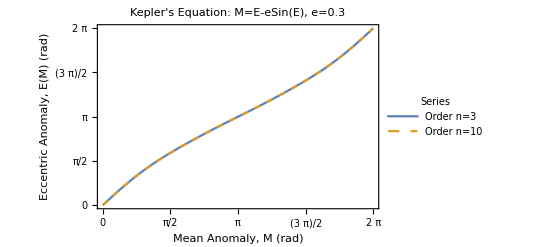

```mathematica
g5=Plot[{J11,J12},{M,0,2*Pi},Frame->True,GridLines->{{0,π/2,π,3 π/2,2 π},{0,π/2,π,3 π/2,2 π}},PlotLabel->"Kepler's Equation: M=E-eSin(E), e=0.3",FrameLabel->{"Mean Anomaly, M (rad)","Eccentric Anomaly, E(M) (rad)"},PlotLegends->LineLegend[{"Order n=3","Order n=10"},LegendLabel->"Series",LegendFunction->Frame],FrameTicks-> {{{0,π/2,π,3 π/2,2 π},None},{{0,π/2,π,3 π/2,2 π},None}},PlotStyle->{Automatic,Dashed}]
```

Plotting of the Fourier - Bessel series expansion for order 3 and 10 for e = 0.9

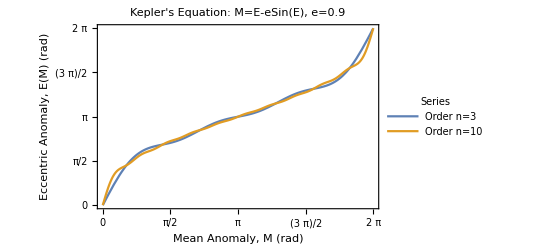

```mathematica
g6=Plot[{J21,J22},{M,0,2*Pi},Frame->True,GridLines->{{0,π/2,π,3 π/2,2 π},{0,π/2,π,3 π/2,2 π}},PlotLabel->"Kepler's Equation: M=E-eSin(E), e=0.9",FrameLabel->{"Mean Anomaly, M (rad)","Eccentric Anomaly, E(M) (rad)"},PlotLegends->LineLegend[{"Order n=3","Order n=10"},LegendLabel->"Series",LegendFunction->Frame],FrameTicks-> {{{0,π/2,π,3 π/2,2 π},None},{{0,π/2,π,3 π/2,2 π},None}}]
```

Comparison of Fourier-Bessel series expansion with the numerical results of Task1

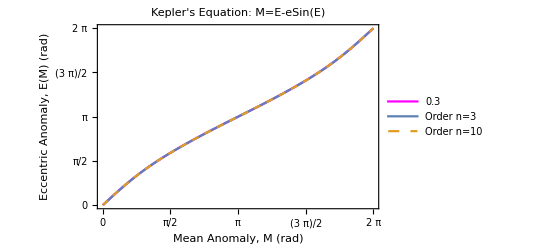

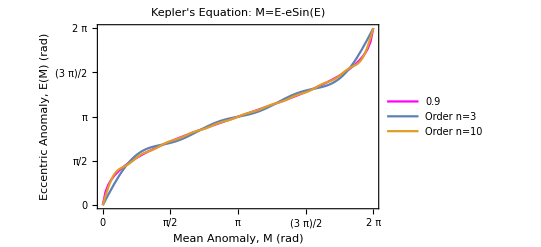

```mathematica
Show[g1,g5]
Show[g2,g6]
```

Rearranging the terms in the Lagrange’s series expansion a new form can be obtained. This form is the Fourier-Bessel series and in this form the coefficients were infinite power series in e which converged for all elliptic orbits. These infinite power series in e are the Bessel functions. Plotting the solutions of Task3 and comparing it with the numerical results of Task1, is evident that for both eccentricities the Fourier-Bessel series converges perfectly for order 10 and sufficiently for order 3. Indeed the effect of altering the order of the terms changed the convergence properties of Lagrange’s expansion.